```mathematica
{hmpkill1np2,hmpkill10np2,hmpkill50np2,hmpkill90np2,hmpkill99np2,hmpkill1np3,hmpkill10np3,hmpkill50np3,hmpkill90np3,hmpkill99np3,hmpkill1np4,hmpkill10np4,hmpkill50np4,hmpkill90np4,hmpkill99np4,hmpkill1np5,hmpkill10np5,hmpkill50np5,hmpkill90np5,hmpkill99np5}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hmpnp2to5.mx"];
```

```mathematica
{hypkill1np2,hypkill10np2,hypkill50np2,hypkill90np2,hypkill99np2,hypkill1np3,hypkill10np3,hypkill50np3,hypkill90np3,hypkill99np3,hypkill1np4,hypkill10np4,hypkill50np4,hypkill90np4,hypkill99np4,hypkill1np5,hypkill10np5,hypkill50np5,hypkill90np5,hypkill99np5}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hypnp2to5.mx"];
```

```mathematica
{hmukill1np2,hmukill50np2,hmukill99np2,hmukill7000np2,hmukill14000np2,hmukill1np3,hmukill50np3,hmukill99np3,hmukill7000np3,hmukill14000np3,hmukill1np4,hmukill50np4,hmukill99np4,hmukill7000np4,hmukill14000np4,hmukill1np5,hmukill50np5,hmukill99np5,hmukill7000np5,hmukill14000np5}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hmunp2to5.mx"];
```

```mathematica
{hpkill1np2,hpkill50np2,hpkill99np2,hpkill3000np2,hpkill6000np2,hpkill1np3,hpkill50np3,hpkill99np3,hpkill3000np3,hpkill6000np3,hpkill1np4,hpkill50np4,hpkill99np4,hpkill3000np4,hpkill6000np4,hpkill1np5,hpkill50np5,hpkill99np5,hpkill3000np5,hpkill6000np5}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hpnp2to5.mx"];
```

```mathematica
{hptyp1np2,hptyp50np2,hptyp99np2,hptyp3000np2,hptyp6000np2,hptyp1np3,hptyp50np3,hptyp99np3,hptyp3000np3,hptyp6000np3,hptyp1np4,hptyp50np4,hptyp99np4,hptyp3000np4,hptyp6000np4,hptyp1np5,hptyp50np5,hptyp99np5,hptyp3000np5,hptyp6000np5}=Parallelize[{titeryieldproductivity[hpkill1np2],titeryieldproductivity[hpkill50np2],titeryieldproductivity[hpkill99np2],titeryieldproductivity[hpkill3000np2],titeryieldproductivity[hpkill6000np2],titeryieldproductivity[hpkill1np3],titeryieldproductivity[hpkill50np3],titeryieldproductivity[hpkill99np3],titeryieldproductivity[hpkill3000np3],titeryieldproductivity[hpkill6000np3],titeryieldproductivity[hpkill1np4],titeryieldproductivity[hpkill50np4],titeryieldproductivity[hpkill99np4],titeryieldproductivity[hpkill3000np4],titeryieldproductivity[hpkill6000np4],titeryieldproductivity[hpkill1np5],titeryieldproductivity[hpkill50np5],titeryieldproductivity[hpkill99np5],titeryieldproductivity[hpkill3000np5],titeryieldproductivity[hpkill6000np5]}];
```

```mathematica
{hpkill3000,hpkill6000,hptyp3000,hptyp6000}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hplargecorrect.mx"];
```

```mathematica
{ol500c24h,ol500c24hkeep,ol500c24hkill,ol500c24hmem,oltyp}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\ol500c24htest.mx"];
```

```mathematica
hpnp={{hptyp1[[2]]/oltyp[[2]],hptyp1np2[[2]]/oltyp[[2]],hptyp1np3[[2]]/oltyp[[2]],hptyp1np4[[2]]/oltyp[[2]],hptyp1np5[[2]]/oltyp[[2]]},{hptyp50[[2]]/oltyp[[2]],hptyp50np2[[2]]/oltyp[[2]],hptyp50np3[[2]]/oltyp[[2]],hptyp50np4[[2]]/oltyp[[2]],hptyp50np5[[2]]/oltyp[[2]]},{hptyp99[[2]]/oltyp[[2]],hptyp99np2[[2]]/oltyp[[2]],hptyp99np3[[2]]/oltyp[[2]],hptyp99np4[[2]]/oltyp[[2]],hptyp99np5[[2]]/oltyp[[2]]},{hptyp3000[[2]]/oltyp[[2]],hptyp3000np2[[2]]/oltyp[[2]],hptyp3000np3[[2]]/oltyp[[2]],hptyp3000np4[[2]]/oltyp[[2]],hptyp3000np5[[2]]/oltyp[[2]]},{hptyp6000[[2]]/oltyp[[2]],hptyp6000np2[[2]]/oltyp[[2]],hptyp6000np3[[2]]/oltyp[[2]],hptyp6000np4[[2]]/oltyp[[2]],hptyp6000np5[[2]]/oltyp[[2]]}}
```

{{1.22623,1.12492,1.06971,1.06599,1.02091},{1.40793,1.32137,1.29027,1.2421,1.23014},{1.61678,1.62917,1.65019,1.68772,1.68875},{2.62064,1.20347,0.632077,0.440604,0.357208},{1.68294,0.394069,0.240588,0.186629,0.164769}}

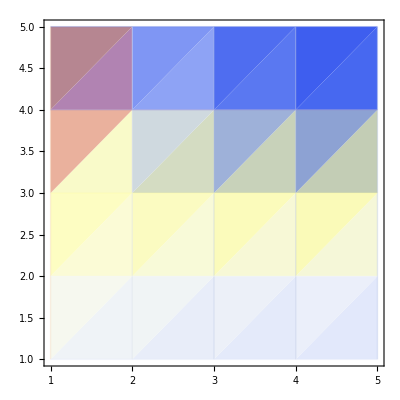

```mathematica
ListDensityPlot[hpnp,Mesh->Full,ColorFunction->"TemperatureMap"]
```

```mathematica
MatrixPlot[hpnp,ColorFunction->"RedBlueTones",PlotLegends->Automatic,FrameTicksStyle->Directive[Black, 16],PlotLegends->Automatic,LabelStyle->Directive[Black, 16]]
```

-Graphics-

```mathematica
ColorData["Gradients"]
```

{AlpineColors,Aquamarine,ArmyColors,AtlanticColors,AuroraColors,AvocadoColors,BeachColors,BlueGreenYellow,BrassTones,BrightBands,BrownCyanTones,CandyColors,CherryTones,CMYKColors,CoffeeTones,DarkBands,DarkRainbow,DarkTerrain,DeepSeaColors,FallColors,FruitPunchColors,FuchsiaTones,GrayTones,GrayYellowTones,GreenBrownTerrain,GreenPinkTones,IslandColors,LakeColors,LightTemperatureMap,LightTerrain,MintColors,NeonColors,Pastel,PearlColors,PigeonTones,PlumColors,Rainbow,RedBlueTones,RedGreenSplit,RoseColors,RustTones,SandyTerrain,SiennaTones,SolarColors,SouthwestColors,StarryNightColors,SunsetColors,TemperatureMap,ThermometerColors,ValentineTones,WatermelonColors}

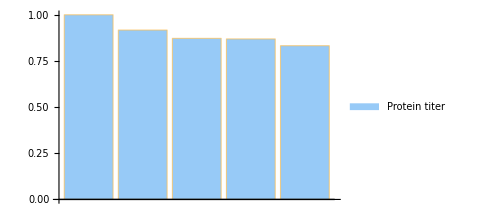

```mathematica
BarChart[{hptyp1[[2]]/hptyp1[[2]],hptyp1np2[[2]]/hptyp1[[2]],hptyp1np3[[2]]/hptyp1[[2]],hptyp1np4[[2]]/hptyp1[[2]],hptyp1np5[[2]]/hptyp1[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#97caf7"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

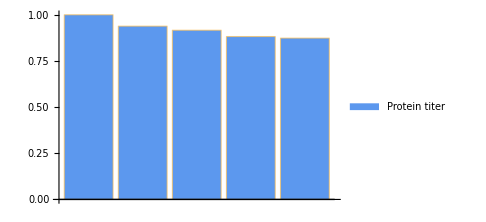

```mathematica
BarChart[{hptyp50[[2]]/hptyp50[[2]],hptyp50np2[[2]]/hptyp50[[2]],hptyp50np3[[2]]/hptyp50[[2]],hptyp50np4[[2]]/hptyp50[[2]],hptyp50np5[[2]]/hptyp50[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#5c98ee"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

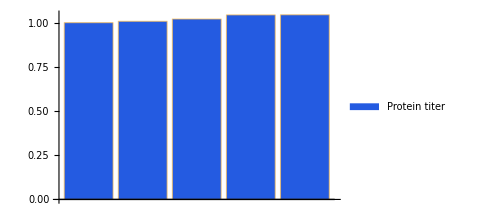

```mathematica
BarChart[{hptyp99[[2]]/hptyp99[[2]],hptyp99np2[[2]]/hptyp99[[2]],hptyp99np3[[2]]/hptyp99[[2]],hptyp99np4[[2]]/hptyp99[[2]],hptyp99np5[[2]]/hptyp99[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{
RGBColor["#245be1"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

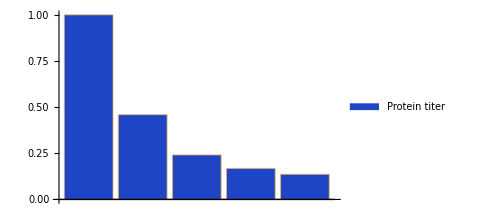

```mathematica
BarChart[{hptyp3000[[2]]/hptyp3000[[2]],hptyp3000np2[[2]]/hptyp3000[[2]],hptyp3000np3[[2]]/hptyp3000[[2]],hptyp3000np4[[2]]/hptyp3000[[2]],hptyp3000np5[[2]]/hptyp3000[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{
RGBColor["#1e45c5"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

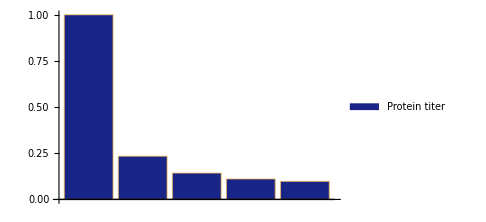

```mathematica
BarChart[{hptyp6000[[2]]/hptyp6000[[2]],hptyp6000np2[[2]]/hptyp6000[[2]],hptyp6000np3[[2]]/hptyp6000[[2]],hptyp6000np4[[2]]/hptyp6000[[2]],hptyp6000np5[[2]]/hptyp6000[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{
RGBColor["#192586"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
{hmutyp1np2,hmutyp50np2,hmutyp99np2,hmutyp7000np2,hmutyp14000np2,hmutyp1np3,hmutyp50np3,hmutyp99np3,hmutyp7000np3,hmutyp14000np3,hmutyp1np4,hmutyp50np4,hmutyp99np4,hmutyp7000np4,hmutyp14000np4,hmutyp1np5,hmutyp50np5,hmutyp99np5,hmutyp7000np5,hmutyp14000np5}=Parallelize[{titeryieldproductivity[hmukill1np2],titeryieldproductivity[hmukill50np2],titeryieldproductivity[hmukill99np2],titeryieldproductivity[hmukill7000np2],titeryieldproductivity[hmukill14000np2],titeryieldproductivity[hmukill1np3],titeryieldproductivity[hmukill50np3],titeryieldproductivity[hmukill99np3],titeryieldproductivity[hmukill7000np3],titeryieldproductivity[hmukill14000np3],titeryieldproductivity[hmukill1np4],titeryieldproductivity[hmukill50np4],titeryieldproductivity[hmukill99np4],titeryieldproductivity[hmukill7000np4],titeryieldproductivity[hmukill14000np4],titeryieldproductivity[hmukill1np5],titeryieldproductivity[hmukill50np5],titeryieldproductivity[hmukill99np5],titeryieldproductivity[hmukill7000np5],titeryieldproductivity[hmukill14000np5]}]
```

{1}
 |  |  |  |

```mathematica
hmunp={{hmutyp1[[2]]/oltyp[[2]],hmutyp1np2[[2]]/oltyp[[2]],hmutyp1np3[[2]]/oltyp[[2]],hmutyp1np4[[2]]/oltyp[[2]],hmutyp1np5[[2]]/oltyp[[2]]},{hmutyp50[[2]]/oltyp[[2]],hmutyp50np2[[2]]/oltyp[[2]],hmutyp50np3[[2]]/oltyp[[2]],hmutyp50np4[[2]]/oltyp[[2]],hmutyp50np5[[2]]/oltyp[[2]]},{hmutyp99[[2]]/oltyp[[2]],hmutyp99np2[[2]]/oltyp[[2]],hmutyp99np3[[2]]/oltyp[[2]],hmutyp99np4[[2]]/oltyp[[2]],hmutyp99np5[[2]]/oltyp[[2]]},{hmutyp7000[[2]]/oltyp[[2]],hmutyp7000np2[[2]]/oltyp[[2]],hmutyp7000np3[[2]]/oltyp[[2]],hmutyp7000np4[[2]]/oltyp[[2]],hmutyp7000np5[[2]]/oltyp[[2]]},{hmutyp14000[[2]]/oltyp[[2]],hmutyp14000np2[[2]]/oltyp[[2]],hmutyp14000np3[[2]]/oltyp[[2]],hmutyp14000np4[[2]]/oltyp[[2]],hmutyp14000np5[[2]]/oltyp[[2]]}}
```

{{1.37542,1.24694,1.18092,1.14256,1.11042},{1.47615,1.42233,1.38317,1.35935,1.35223},{1.62125,1.68526,1.72191,1.75194,1.79488},{1.3768,0.211622,0.141193,0.131072,0.128572},{0.48635,0.146956,0.129192,0.1289,0.128193}}

```mathematica
MatrixPlot[hmunp,ColorFunction->"AvocadoColors",PlotLegends->Automatic,FrameTicksStyle->Directive[Black, 16],PlotLegends->Automatic,LabelStyle->Directive[Black, 16]]
```

-Graphics-

```mathematica
MatrixPlot[hmunp,ColorFunction->"BlueGreenYellow",PlotLegends->Automatic,FrameTicksStyle->Directive[Black, 16],PlotLegends->Automatic,LabelStyle->Directive[Black, 16]]
```

-Graphics-

```mathematica
{hmugen1,hmugen10,hmugen50,hmugen90,hmugen99,hmukeep1,hmukeep10,hmukeep50,hmukeep90,hmukeep99,hmumem1,hmumem10,hmumem50,hmumem90,hmumem99,hmukill1,hmukill10,hmukill50,hmukill90,hmukill99,hmutyp1,hmutyp10,hmutyp50,hmutyp90,hmutyp99}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hmu500c24hpercent.mx"];
```

```mathematica
hmutyp7000=titeryieldproductivity[hmukill7000];
```

```mathematica
hmutyp14000=titeryieldproductivity[hmukill14000];
```

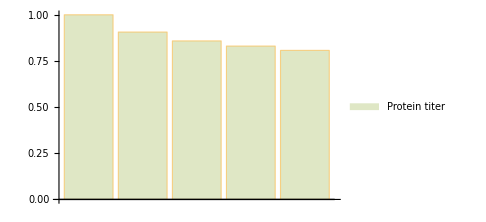

```mathematica
BarChart[{hmutyp1[[2]]/hmutyp1[[2]],hmutyp1np2[[2]]/hmutyp1[[2]],hmutyp1np3[[2]]/hmutyp1[[2]],hmutyp1np4[[2]]/hmutyp1[[2]],hmutyp1np5[[2]]/hmutyp1[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#dfe7c5"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

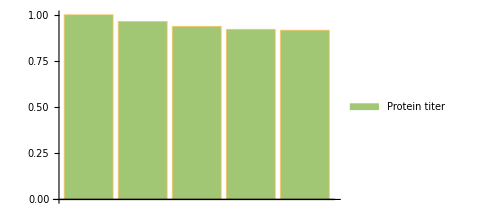

```mathematica
BarChart[{hmutyp50[[2]]/hmutyp50[[2]],hmutyp50np2[[2]]/hmutyp50[[2]],hmutyp50np3[[2]]/hmutyp50[[2]],hmutyp50np4[[2]]/hmutyp50[[2]],hmutyp50np5[[2]]/hmutyp50[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#a1c774"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

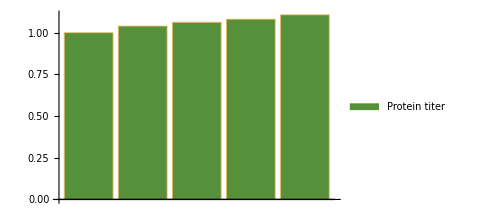

```mathematica
BarChart[{hmutyp99[[2]]/hmutyp99[[2]],hmutyp99np2[[2]]/hmutyp99[[2]],hmutyp99np3[[2]]/hmutyp99[[2]],hmutyp99np4[[2]]/hmutyp99[[2]],hmutyp99np5[[2]]/hmutyp99[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#56903a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

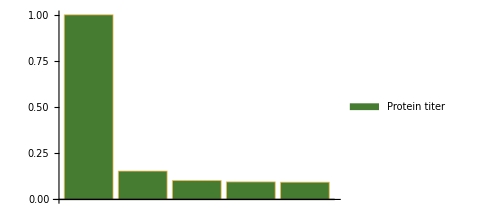

```mathematica
BarChart[{hmutyp7000[[2]]/hmutyp7000[[2]],hmutyp7000np2[[2]]/hmutyp7000[[2]],hmutyp7000np3[[2]]/hmutyp7000[[2]],hmutyp7000np4[[2]]/hmutyp7000[[2]],hmutyp7000np5[[2]]/hmutyp7000[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#457c31"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

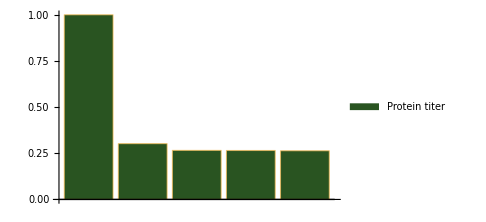

```mathematica
BarChart[{hmutyp14000[[2]]/hmutyp14000[[2]],hmutyp14000np2[[2]]/hmutyp14000[[2]],hmutyp14000np3[[2]]/hmutyp14000[[2]],hmutyp14000np4[[2]]/hmutyp14000[[2]],hmutyp14000np5[[2]]/hmutyp14000[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#295421"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
{hyptyp1np2,hyptyp10np2,hyptyp50np2,hyptyp90np2,hyptyp99np2,hyptyp1np3,hyptyp10np3,hyptyp50np3,hyptyp90np3,hyptyp99np3,hyptyp1np4,hyptyp10np4,hyptyp50np4,hyptyp90np4,hyptyp99np4,hyptyp1np5,hyptyp10np5,hyptyp50np5,hyptyp90np5,hyptyp99np5}=Parallelize[{titeryieldproductivity[hypkill1np2],titeryieldproductivity[hypkill10np2],titeryieldproductivity[hypkill50np2],titeryieldproductivity[hypkill90np2],titeryieldproductivity[hypkill99np2],titeryieldproductivity[hypkill1np3],titeryieldproductivity[hypkill10np3],titeryieldproductivity[hypkill50np3],titeryieldproductivity[hypkill90np3],titeryieldproductivity[hypkill99np3],titeryieldproductivity[hypkill1np4],titeryieldproductivity[hypkill10np4],titeryieldproductivity[hypkill50np4],titeryieldproductivity[hypkill90np4],titeryieldproductivity[hypkill99np4],titeryieldproductivity[hypkill1np5],titeryieldproductivity[hypkill10np5],titeryieldproductivity[hypkill50np5],titeryieldproductivity[hypkill90np5],titeryieldproductivity[hypkill99np5]}];
```

```mathematica
{hypgen1,hypgen10,hypgen50,hypgen90,hypgen99,hypkeep1,hypkeep10,hypkeep50,hypkeep90,hypkeep99,hypmem1,hypmem10,hypmem50,hypmem90,hypmem99,hypkill1,hypkill10,hypkill50,hypkill90,hypkill99,hyptyp1,hyptyp10,hyptyp50,hyptyp90,hyptyp99}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hyp500c24hpercent.mx"];
```

```mathematica
hypnp={{hyptyp1[[2]]/oltyp[[2]],hyptyp1np2[[2]]/oltyp[[2]],hyptyp1np3[[2]]/oltyp[[2]],hyptyp1np4[[2]]/oltyp[[2]],hyptyp1np5[[2]]/oltyp[[2]]},{hyptyp10[[2]]/oltyp[[2]],hyptyp10np2[[2]]/oltyp[[2]],hyptyp10np3[[2]]/oltyp[[2]],hyptyp10np4[[2]]/oltyp[[2]],hyptyp10np5[[2]]/oltyp[[2]]},{hyptyp50[[2]]/oltyp[[2]],hyptyp50np2[[2]]/oltyp[[2]],hyptyp50np3[[2]]/oltyp[[2]],hyptyp50np4[[2]]/oltyp[[2]],hyptyp50np5[[2]]/oltyp[[2]]},{hyptyp90[[2]]/oltyp[[2]],hyptyp90np2[[2]]/oltyp[[2]],hyptyp90np3[[2]]/oltyp[[2]],hyptyp90np4[[2]]/oltyp[[2]],hyptyp90np5[[2]]/oltyp[[2]]},{hyptyp99[[2]]/oltyp[[2]],hyptyp99np2[[2]]/oltyp[[2]],hyptyp99np3[[2]]/oltyp[[2]],hyptyp99np4[[2]]/oltyp[[2]],hyptyp99np5[[2]]/oltyp[[2]]}}
```

{{1.54437,1.80959,1.92655,1.96203,1.96818},{1.23916,1.46373,1.59305,1.65788,1.73066},{0.968054,0.97507,0.969392,0.966567,0.921248},{0.814283,0.641928,0.548644,0.446205,0.410168},{0.655847,0.434595,0.2568,0.176427,0.123239}}

```mathematica
MatrixPlot[hypnp,ColorFunction->"GreenPinkTones",PlotLegends->Automatic,FrameTicksStyle->Directive[Black, 16],PlotLegends->Automatic,LabelStyle->Directive[Black, 16]]
```

-Graphics-

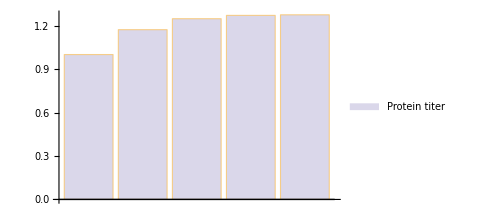

```mathematica
BarChart[{hyptyp1[[2]]/hyptyp1[[2]],hyptyp1np2[[2]]/hyptyp1[[2]],hyptyp1np3[[2]]/hyptyp1[[2]],hyptyp1np4[[2]]/hyptyp1[[2]],hyptyp1np5[[2]]/hyptyp1[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#dad7ea"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

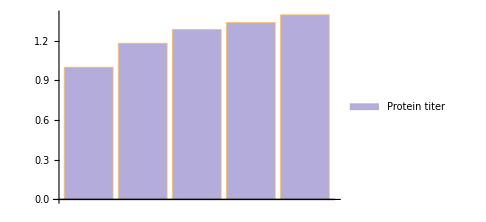

```mathematica
BarChart[{hyptyp10[[2]]/hyptyp10[[2]],hyptyp10np2[[2]]/hyptyp10[[2]],hyptyp10np3[[2]]/hyptyp10[[2]],hyptyp10np4[[2]]/hyptyp10[[2]],hyptyp10np5[[2]]/hyptyp10[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#b4acdb"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

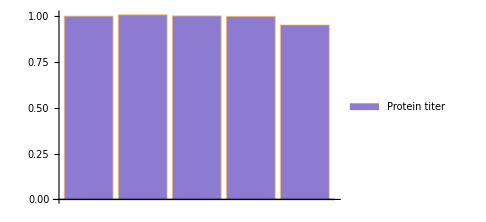

```mathematica
BarChart[{hyptyp50[[2]]/hyptyp50[[2]],hyptyp50np2[[2]]/hyptyp50[[2]],hyptyp50np3[[2]]/hyptyp50[[2]],hyptyp50np4[[2]]/hyptyp50[[2]],hyptyp50np5[[2]]/hyptyp50[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#8c7bd1"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

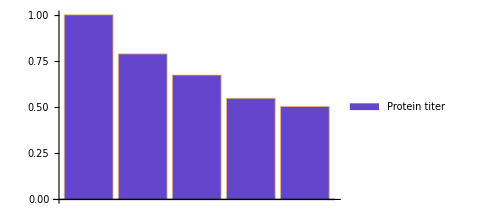

```mathematica
BarChart[{hyptyp90[[2]]/hyptyp90[[2]],hyptyp90np2[[2]]/hyptyp90[[2]],hyptyp90np3[[2]]/hyptyp90[[2]],hyptyp90np4[[2]]/hyptyp90[[2]],hyptyp90np5[[2]]/hyptyp90[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#6446cd"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

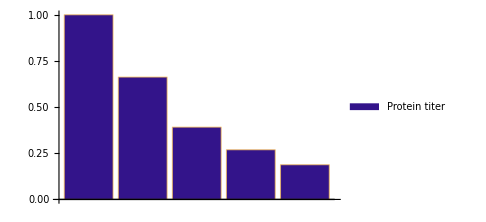

```mathematica
BarChart[{hyptyp99[[2]]/hyptyp99[[2]],hyptyp99np2[[2]]/hyptyp99[[2]],hyptyp99np3[[2]]/hyptyp99[[2]],hyptyp99np4[[2]]/hyptyp99[[2]],hyptyp99np5[[2]]/hyptyp99[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#33148a"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

```mathematica
{hmptyp1np2,hmptyp10np2,hmptyp50np2,hmptyp90np2,hmptyp99np2,hmptyp1np3,hmptyp10np3,hmptyp50np3,hmptyp90np3,hmptyp99np3,hmptyp1np4,hmptyp10np4,hmptyp50np4,hmptyp90np4,hmptyp99np4,hmptyp1np5,hmptyp10np5,hmptyp50np5,hmptyp90np5,hmptyp99np5}=Parallelize[{titeryieldproductivity[hmpkill1np2],titeryieldproductivity[hmpkill10np2],titeryieldproductivity[hmpkill50np2],titeryieldproductivity[hmpkill90np2],titeryieldproductivity[hmpkill99np2],titeryieldproductivity[hmpkill1np3],titeryieldproductivity[hmpkill10np3],titeryieldproductivity[hmpkill50np3],titeryieldproductivity[hmpkill90np3],titeryieldproductivity[hmpkill99np3],titeryieldproductivity[hmpkill1np4],titeryieldproductivity[hmpkill10np4],titeryieldproductivity[hmpkill50np4],titeryieldproductivity[hmpkill90np4],titeryieldproductivity[hmpkill99np4],titeryieldproductivity[hmpkill1np5],titeryieldproductivity[hmpkill10np5],titeryieldproductivity[hmpkill50np5],titeryieldproductivity[hmpkill90np5],titeryieldproductivity[hmpkill99np5]}];
```

```mathematica
{hmpgen1,hmpgen10,hmpgen50,hmpgen90,hmpgen99,hmpkeep1,hmpkeep10,hmpkeep50,hmpkeep90,hmpkeep99,hmpmem1,hmpmem10,hmpmem50,hmpmem90,hmpmem99,hmpkill1,hmpkill10,hmpkill50,hmpkill90,hmpkill99,hmptyp1,hmptyp10,hmptyp50,hmptyp90,hmptyp99}=Import["C:\\Users\\mxy\\Desktop\\Modeling paper\\hmp500c24hpercent.mx"];
```

```mathematica
hmpnp={{hmptyp1[[2]]/oltyp[[2]],hmptyp1np2[[2]]/oltyp[[2]],hmptyp1np3[[2]]/oltyp[[2]],hmptyp1np4[[2]]/oltyp[[2]],hmptyp1np5[[2]]/oltyp[[2]]},{hmptyp10[[2]]/oltyp[[2]],hmptyp10np2[[2]]/oltyp[[2]],hmptyp10np3[[2]]/oltyp[[2]],hmptyp10np4[[2]]/oltyp[[2]],hmptyp10np5[[2]]/oltyp[[2]]},{hmptyp50[[2]]/oltyp[[2]],hmptyp50np2[[2]]/oltyp[[2]],hmptyp50np3[[2]]/oltyp[[2]],hmptyp50np4[[2]]/oltyp[[2]],hmptyp50np5[[2]]/oltyp[[2]]},{hmptyp90[[2]]/oltyp[[2]],hmptyp90np2[[2]]/oltyp[[2]],hmptyp90np3[[2]]/oltyp[[2]],hmptyp90np4[[2]]/oltyp[[2]],hmptyp90np5[[2]]/oltyp[[2]]},{hmptyp99[[2]]/oltyp[[2]],hmptyp99np2[[2]]/oltyp[[2]],hmptyp99np3[[2]]/oltyp[[2]],hmptyp99np4[[2]]/oltyp[[2]],hmptyp99np5[[2]]/oltyp[[2]]}}
```

{{1.15878,1.2888,1.44874,1.53842,1.63265},{1.05048,1.1504,1.20004,1.26992,1.33649},{0.994253,1.01062,0.99728,0.994725,0.970968},{0.935238,0.882512,0.795956,0.67762,0.605656},{0.846167,0.686614,0.554025,0.427155,0.269267}}

```mathematica
MatrixPlot[hmpnp,ColorFunction->"ThermometerColors",PlotLegends->Automatic,FrameTicksStyle->Directive[Black, 16],PlotLegends->Automatic,LabelStyle->Directive[Black, 16]]
```

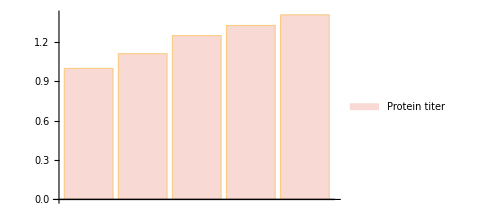

```mathematica
BarChart[{hmptyp1[[2]]/hmptyp1[[2]],hmptyp1np2[[2]]/hmptyp1[[2]],hmptyp1np3[[2]]/hmptyp1[[2]],hmptyp1np4[[2]]/hmptyp1[[2]],hmptyp1np5[[2]]/hmptyp1[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#f8d9d3"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

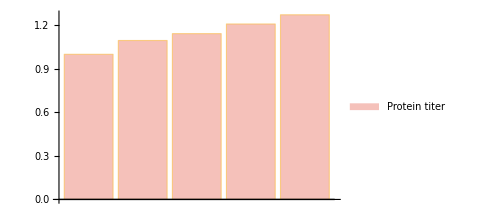

```mathematica
BarChart[{hmptyp10[[2]]/hmptyp10[[2]],hmptyp10np2[[2]]/hmptyp10[[2]],hmptyp10np3[[2]]/hmptyp10[[2]],hmptyp10np4[[2]]/hmptyp10[[2]],hmptyp10np5[[2]]/hmptyp10[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#f5c1ba"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

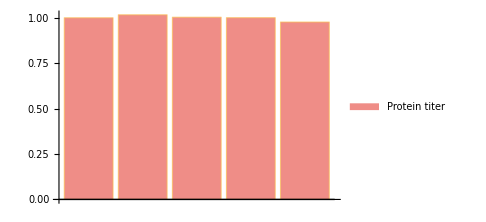

```mathematica
BarChart[{hmptyp50[[2]]/hmptyp50[[2]],hmptyp50np2[[2]]/hmptyp50[[2]],hmptyp50np3[[2]]/hmptyp50[[2]],hmptyp50np4[[2]]/hmptyp50[[2]],hmptyp50np5[[2]]/hmptyp50[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#ef8d87"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

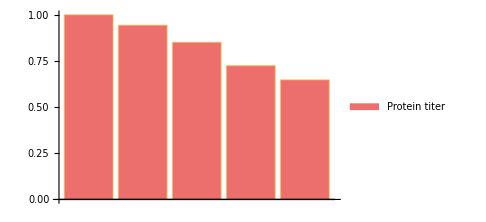

```mathematica
BarChart[{hmptyp90[[2]]/hmptyp90[[2]],hmptyp90np2[[2]]/hmptyp90[[2]],hmptyp90np3[[2]]/hmptyp90[[2]],hmptyp90np4[[2]]/hmptyp90[[2]],hmptyp90np5[[2]]/hmptyp90[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#ed6f6d"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```

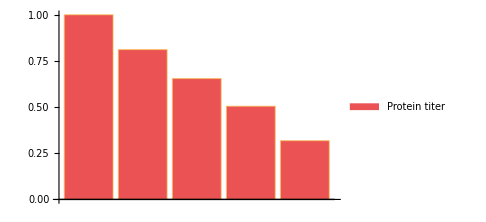

```mathematica
BarChart[{hmptyp99[[2]]/hmptyp99[[2]],hmptyp99np2[[2]]/hmptyp99[[2]],hmptyp99np3[[2]]/hmptyp99[[2]],hmptyp99np4[[2]]/hmptyp99[[2]],hmptyp99np5[[2]]/hmptyp99[[2]]},ChartLegends->{"Protein titer"},ChartStyle->{RGBColor["#eb5254"]},AxesStyle->Directive[Black, 16],ImageSize->Medium]
```